## Matrix Element calculation (including time evolution)

```mathematica
Clear[ω,ωt,t]
```

```mathematica
L =3.*10^-7; Lstep =1.*10^-8; LN = 2.*L/Lstep + 1.;nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[x_,xt_,t_,ωt_]:= ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)]
deltak = 20 Pi/(455 10^-9)//N
ψ[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]
ψf[xt_, nt_, ωt_]:= 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]
```

1.38092×10^8

```mathematica
Export["/home/julian/Schreibtisch/export.png",Plot[Re[ψ[x,2,10^7]],{x,-L,L}, PlotRange-> All, Axes -> None, PlotStyle -> Directive[{Darker[Green], Thickness[0.02]}]],Background->None]
```

/home/julian/Schreibtisch/export.png

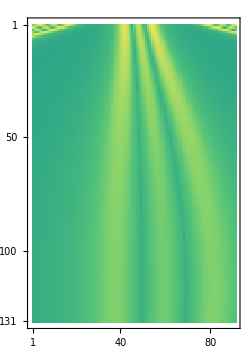

```mathematica
L =0.9*10^-7; Lstep =0.2*10^-8; LN = 2*L/Lstep + 1;
psi[t_, xt_,ω_,ωt_, n_] :=  Lstep*Sum[ψ[x, n, ω]*  Uprop[x,xt,t,ωt],{x,-L,L,Lstep}]
Monitor[evolmat = Table[Abs[psi[t, xt,10^7,0.25*10^7, 2]]^2,{t,50 10^-9,700 10^-9, 5 10^-9},{xt, -L, L, Lstep}];,{(t/(400 10^-9))//N,(xt/L)}]
MatrixPlot[evolmat, ColorFunction->"BlueGreenYellow"]
```

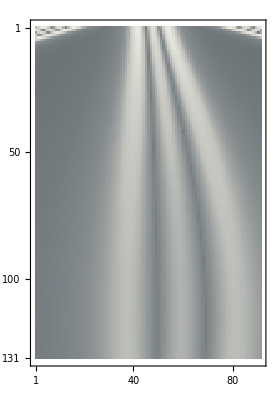

```mathematica
MatrixPlot[evolmat, ColorFunction->"GrayTones",ColorFunctionScaling->True]
```

```mathematica
xticks=Transpose[{Range@91,Table[g, {g,-90,90,1.0000001 180/91//N}]}]
yticks=Transpose[{Range@131,Table[g, {g,0,700,1.0000001 700/131//N}]}]
```

{{1,-90.},{2,-88.022},{3,-86.044},{4,-84.0659},{5,-82.0879},{6,-80.1099},{7,-78.1319},{8,-76.1538},{9,-74.1758},{10,-72.1978},{11,-70.2198},{12,-68.2418},{13,-66.2637},{14,-64.2857},{15,-62.3077},{16,-60.3297},{17,-58.3516},{18,-56.3736},{19,-54.3956},{20,-52.4176},{21,-50.4396},{22,-48.4615},{23,-46.4835},{24,-44.5055},{25,-42.5275},{26,-40.5494},{27,-38.5714},{28,-36.5934},{29,-34.6154},{30,-32.6374},{31,-30.6593},{32,-28.6813},{33,-26.7033},{34,-24.7253},{35,-22.7472},{36,-20.7692},{37,-18.7912},{38,-16.8132},{39,-14.8352},{40,-12.8571},{41,-10.8791},{42,-8.90109},{43,-6.92307},{44,-4.94505},{45,-2.96702},{46,-0.989002},{47,0.98902},{48,2.96704},{49,4.94506},{50,6.92309},{51,8.90111},{52,10.8791},{53,12.8572},{54,14.8352},{55,16.8132},{56,18.7912},{57,20.7692},{58,22.7473},{59,24.7253},{60,26.7033},{61,28.6813},{62,30.6594},{63,32.6374},{64,34.6154},{65,36.5934},{66,38.5714},{67,40.5495},{68,42.5275},{69,44.5055},{70,46.4835},{71,48.4616},{72,50.4396},{73,52.4176},{74,54.3956},{75,56.3736},{76,58.3517},{77,60.3297},{78,62.3077},{79,64.2857},{80,66.2638},{81,68.2418},{82,70.2198},{83,72.1978},{84,74.1758},{85,76.1539},{86,78.1319},{87,80.1099},{88,82.0879},{89,84.066},{90,86.044},{91,88.022}}

{{1,0.},{2,5.34351},{3,10.687},{4,16.0305},{5,21.374},{6,26.7176},{7,32.0611},{8,37.4046},{9,42.7481},{10,48.0916},{11,53.4351},{12,58.7786},{13,64.1221},{14,69.4657},{15,74.8092},{16,80.1527},{17,85.4962},{18,90.8397},{19,96.1832},{20,101.527},{21,106.87},{22,112.214},{23,117.557},{24,122.901},{25,128.244},{26,133.588},{27,138.931},{28,144.275},{29,149.618},{30,154.962},{31,160.305},{32,165.649},{33,170.992},{34,176.336},{35,181.679},{36,187.023},{37,192.366},{38,197.71},{39,203.053},{40,208.397},{41,213.74},{42,219.084},{43,224.428},{44,229.771},{45,235.115},{46,240.458},{47,245.802},{48,251.145},{49,256.489},{50,261.832},{51,267.176},{52,272.519},{53,277.863},{54,283.206},{55,288.55},{56,293.893},{57,299.237},{58,304.58},{59,309.924},{60,315.267},{61,320.611},{62,325.954},{63,331.298},{64,336.641},{65,341.985},{66,347.328},{67,352.672},{68,358.015},{69,363.359},{70,368.702},{71,374.046},{72,379.389},{73,384.733},{74,390.076},{75,395.42},{76,400.763},{77,406.107},{78,411.45},{79,416.794},{80,422.137},{81,427.481},{82,432.824},{83,438.168},{84,443.511},{85,448.855},{86,454.199},{87,459.542},{88,464.886},{89,470.229},{90,475.573},{91,480.916},{92,486.26},{93,491.603},{94,496.947},{95,502.29},{96,507.634},{97,512.977},{98,518.321},{99,523.664},{100,529.008},{101,534.351},{102,539.695},{103,545.038},{104,550.382},{105,555.725},{106,561.069},{107,566.412},{108,571.756},{109,577.099},{110,582.443},{111,587.786},{112,593.13},{113,598.473},{114,603.817},{115,609.16},{116,614.504},{117,619.847},{118,625.191},{119,630.534},{120,635.878},{121,641.221},{122,646.565},{123,651.908},{124,657.252},{125,662.595},{126,667.939},{127,673.283},{128,678.626},{129,683.97},{130,689.313},{131,694.657}}

```mathematica
nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.4*10^-7; Lstep =0.2*10^-8; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
UPn[ω_, ωt_,n_, nt_, t_] := Lstep^2 *Sum[ 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]
```

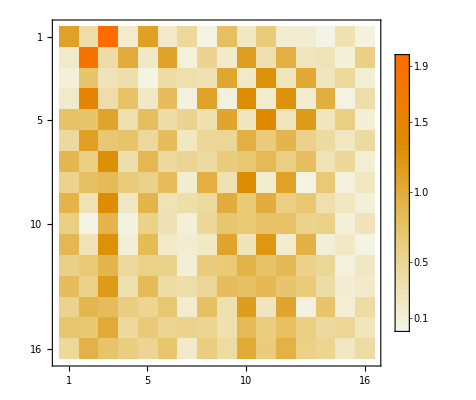

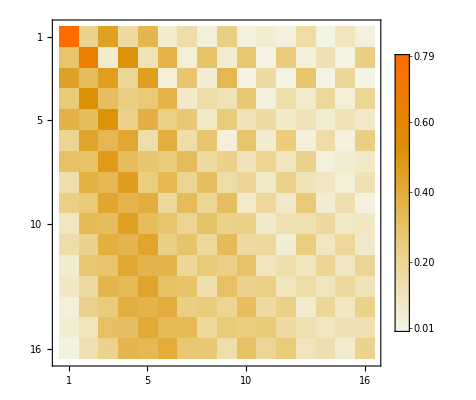

```mathematica
Monitor[t= 20 10^-9; ω =10^7 ;ωt =0.25*10^7;uma2 = Table[Abs[Lstep^2 *Sum[ 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x] ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma2, PlotLegends -> True]
Monitor[ω = 10^7; ωt=0.25*10^7; t= 500 10^-9;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,2*10^7,n,nt,250*10^-9]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

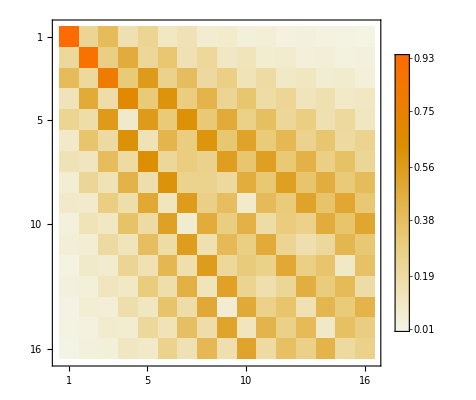

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,2*10^7,n,nt,20]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

```mathematica
uma -uma2
```

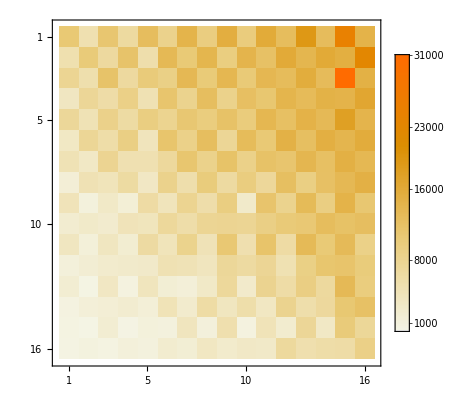

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,1.3*10^7,n,nt,537*10^-9]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

```mathematica
Monitor[uma = Table[Abs[UPn[1.*10^7,2*10^7,n,nt,250.*10^-9]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

$Aborted

-Graphics-

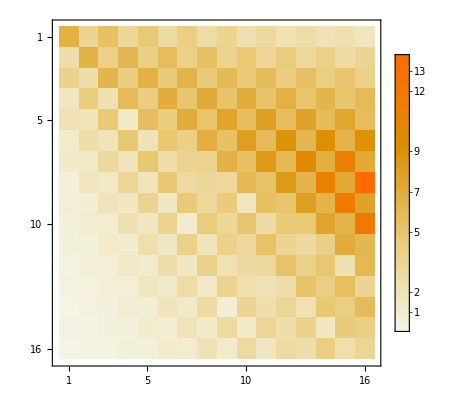

```mathematica
Monitor[ω = 10^7; ωt=2*10^7; t= 250 10^-9;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^n nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

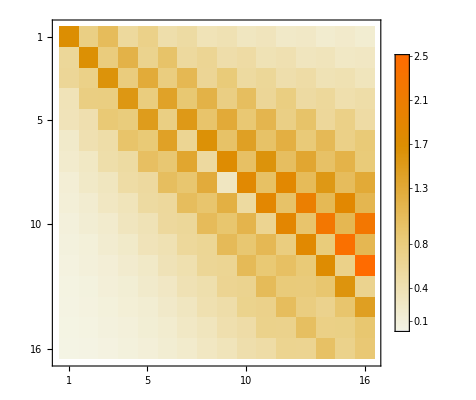

```mathematica
Monitor[ω = 10^7; ωt=0.7*10^7; t= 532 10^-9;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^n nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

```mathematica
Total[uma[[5]]]
```

2.01507

## Calculate matrix elements for all segments

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]
eta[n_]:= etas[[n]]
nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.4*10^-7; Lstep =0.2*10^-8; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
Clear[t]
```

```mathematica
IntU[ω_,ωt_,τ_]:= Monitor[tstart = τ/10;tstop = 3*τ //N; tstep =(tstop/5)//N;Sum[uma = tstep*Table[Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] Exp[-t/τ]/τ,{t,tstart, tstop, tstep}],{n,nt,t//N}]
```

```mathematica
U12= IntU[omegas[1],omegas[2], (1/g21) //N]
U23 = IntU[omegas[2],omegas[3], (1/g23) //N]
U35 = IntU[omegas[3],omegas[5], (1/g35) //N]
U41 = IntU[omegas[4],omegas[1], (1/g41) //N]
U64 = IntU[omegas[6],omegas[4], (1/g64) //N]
U51 = IntU[omegas[5],omegas[1], (1/g51) //N]
U65 = IntU[omegas[6],omegas[5], (1/g65) //N]
U75 = IntU[omegas[7],omegas[5], (1/g75) //N]
U27 = IntU[omegas[2],omegas[7], (1/g27) //N]
U26 = IntU[omegas[2],omegas[6], (1/g26) //N]
U34 = IntU[omegas[3],omegas[4], (1/g34) //N]
```

```mathematica
U12= IntU[omegas[1],omegas[2], (1/g21) //N]
```

$Aborted